## Parameters, data and the next generation matrix

The parameters, the data and NGM at chi = 0 are in settings_zf_jg.wl, in this directory; the next cell loads them. min_rho_single_dose_H_ZF_JG.nb loads the same file.

```mathematica
Get[FileNameJoin[{NotebookDirectory[], "settings_zf_jg.wl"}]]
```

```mathematica
Export["NGM.csv",NGM];
```

```mathematica
Dimensions[NGM]
```

```mathematica
Re[Eigenvalues[NGM,17]]
```

```mathematica
Abs[Eigenvectors[NGM,1]]
```

```mathematica
Abs[Eigenvectors[Transpose[NGM],1]]
```

```mathematica
Re[Eigenvalues[NGM,1]]
```

## John' s method

```mathematica
Re[Eigenvalues[NGM,1]]
```

{4.42307}

```mathematica
Psdfe0=Table[1,{i,1,m},{j,1,n}]//Quiet;
RN={"Northeast","Midwest","South","West"};
```

```mathematica
T=Table[Partition[Flatten[Abs[Eigenvectors[Transpose[NGM],1]]],2 n][[k]],{k,1,m}] ;
 l0=Table[Table[Psdfe0[[i, j]]×T[[i,2 j-1]]+0×T[[i,2 j]], {j,1,n}],{i,1,m}];
dTcks={{1,"0-19"},{2,"20-39"},{3,"40-59"},{4,"60+"}};
```

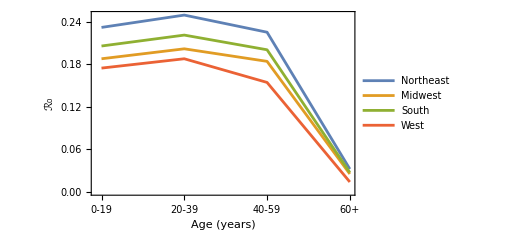

```mathematica
f11=ListPlot[Table[Tooltip[ l0[[i]],RN[[i]]],{i,1,m}],PlotMarkers->None,Joined->True,PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"Age (years)","ℛ_0"},FrameTicks->{{Automatic,Automatic},{dTcks,None}},PlotLegends->RN,LabelStyle->Directive[FontSize->12,FontFamily->"Arial"],ImageSize->375]
```